```mathematica
exp1 = Expand[r*y(1-y/KK) + b*(y^2/(a^2+y^2))]
```

r y-(r y^2)/KK+(b y^2)/(a^2+y^2)

```mathematica
Together[exp1]
```

(a^2 KK r y+b KK y^2-a^2 r y^2+KK r y^3-r y^4)/(KK (a^2+y^2))

```mathematica
exp2 = Expand[rho*z(1-z)+z^2/(1+z^2)]
```

rho z-rho z^2+z^2/(1+z^2)

```mathematica
expanded2  :=Together[exp2]
```

```mathematica
y:=zbar*z
```

```mathematica
expanded1 = Together[exp1]
```

(a^2 KK r z zbar+b KK z^2 zbar^2-a^2 r z^2 zbar^2+KK r z^3 zbar^3-r z^4 zbar^4)/(KK (a^2+z^2 zbar^2))

```mathematica
xExpr := Solve[expanded1*x == expanded2,x]
```

```mathematica
xExpr
```

{{x→(KK (-rho-z+rho z-rho z^2+rho z^3) (a^2+z^2 zbar^2))/((1+z^2) zbar (-a^2 KK r-b KK z zbar+a^2 r z zbar-KK r z^2 zbar^2+r z^3 zbar^3))}}

```mathematica
xExpr.x
```

{{x→(KK (-rho-z+rho z-rho z^2+rho z^3) (a^2+z^2 zbar^2))/((1+z^2) zbar (-a^2 KK r-b KK z zbar+a^2 r z zbar-KK r z^2 zbar^2+r z^3 zbar^3))}}.x

```mathematica
xExpr->x
```

{{x→(KK (-rho-z+rho z-rho z^2+rho z^3) (a^2+z^2 zbar^2))/((1+z^2) zbar (-a^2 KK r-b KK z zbar+a^2 r z zbar-KK r z^2 zbar^2+r z^3 zbar^3))}}→x

```mathematica
fraction = x/.xExpr
```

{(KK (-rho-z+rho z-rho z^2+rho z^3) (a^2+z^2 zbar^2))/((1+z^2) zbar (-a^2 KK r-b KK z zbar+a^2 r z zbar-KK r z^2 zbar^2+r z^3 zbar^3))}

```mathematica
numer = KK (-rho-z+rho z-rho z^2+rho z^3) (a^2+z^2 zbar^2)
```

KK (-rho-z+rho z-rho z^2+rho z^3) (a^2+z^2 zbar^2)

```mathematica
Factor[Expand[numer]]
```

KK (-rho-z+rho z-rho z^2+rho z^3) (a^2+z^2 zbar^2)

```mathematica
denom = (1+z^2) zbar (-a^2 KK r-b KK z zbar+a^2 r z zbar-KK r z^2 zbar^2+r z^3 zbar^3)
```

(1+z^2) zbar (-a^2 KK r-b KK z zbar+a^2 r z zbar-KK r z^2 zbar^2+r z^3 zbar^3)

```mathematica
Expand[denom]
```

-a^2 KK r zbar-a^2 KK r z^2 zbar-b KK z zbar^2+a^2 r z zbar^2-b KK z^3 zbar^2+a^2 r z^3 zbar^2-KK r z^2 zbar^3-KK r z^4 zbar^3+r z^3 zbar^4+r z^5 zbar^4

```mathematica
Expand[numer]
```

-a^2 KK rho-a^2 KK z+a^2 KK rho z-a^2 KK rho z^2+a^2 KK rho z^3-KK rho z^2 zbar^2-KK z^3 zbar^2+KK rho z^3 zbar^2-KK rho z^4 zbar^2+KK rho z^5 zbar^2

```mathematica
Manipulate[Plot[{rho*z*(1-z)+z^2/(1+z^2)},{z,-1,1.3}],{rho,-3,3}]
```

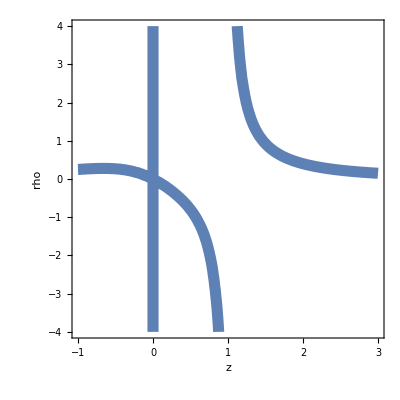

```mathematica
ContourPlot[{rho*z*(1-z)+z^2/(1+z^2)==0},{z,-1,3},{rho,-4,4},AxesLabel->Automatic,ContourStyle->Thickness[.02]]
```

```mathematica
Manipulate[Plot[{-y(y+1)(y-1)-rho},{y,-1,1.3}],{rho,-3,3}]
```